## Prima di cominciare

Prima di cominciare sarà necessario clickare sul pulsante “Enable Dynamics” per permettere il corretto funzionamento della presentazione:

-Graphics-



Successivamente basterà premere “Start Presentation”:

-Graphics-

# Chips-Eaters Tutorial sul calcolo delle probabilità tramite mani di poker

## Gruppi Luca - 0001099394 Raciti Gabriele - 0001102147 Tamai Leonardo - 0001098711

## Introduzione

Questo template ha lo scopo di introdurre l’utente al calcolo della probabilità e farlo esercitare tramite piccoli esercizi basati
sul gioco del poker, che cresceranno man mano di difficoltà. 
Abbiamo realizzato 4 modalità :
 - La prima, molto semplice, consiste nel calcolare la probabilità che esca una coppia rivelando una singola carta coperta dal banco.
 - La seconda, consiste nel calcolare la probabilità che esca un tris rivelando un numero randomico di carte coperte dal banco.
 - La terza, consiste nel calcolare la probabilità che esca una coppia rivelando un numero randomico di carta coperte dal banco.
 - La quarta, consiste nel calcolare la probabilità che esca una coppia rivelando le due carte carte successive del banco e tenendo conto anche delle carte avversarie.

L’utente, dopo aver scelto la modalità alla quale vuole giocare tramite il menù a tendina e aver cliccato su “Nuovo esericizio”,
dovrà inserire il risultato della probabilità richiesta sotto forma di frazione o formula. Successivamente, cliccando su “Verifica risultato”, verrà notificato della correttezza o meno della risposta.
Cliccando sul pulsante “Pulisci esercizio”, avverrà la pulizia del campo di risposta utente e della notifica di correttezza della risposta.
Inoltre, è stato implementato un bottone per la spiegazione dell’esercizio, che ci mostrerà come risolverlo e come calcolare la probabilità richiesta.
E’ anche presente infine una sezione dove inserire il numero di un esercizio già svolto (seed), per poter ripetere gli esercizi passati e cercare di migliorare.

## Preparazione agli esercizi (1)

Un mazzo di Poker è composto da 52 carte divise in 4 semi, dove per ognuno ci sono 13 carte, dal valore che va da 1 a K.

```mathematica
Print[ResourceFunction["PlayingCardGraphic"][1,ImageSize->{100,150}]ResourceFunction["PlayingCardGraphic"][14,ImageSize->{100,150}]ResourceFunction["PlayingCardGraphic"][27,ImageSize->{100,150}]ResourceFunction["PlayingCardGraphic"][40,ImageSize->{100,150}]]
```

I semi sono i seguenti:

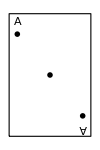
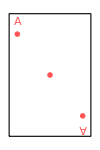
-Graphics- -Graphics- -Graphics- -Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][1,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][2,ImageSize->{100,150}],"  ",
ResourceFunction["PlayingCardGraphic"][3,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][4,ImageSize->{100,150}],"  ",
ResourceFunction["PlayingCardGraphic"][5,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][6,ImageSize->{100,150}],"  ",
ResourceFunction["PlayingCardGraphic"][7,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][8,ImageSize->{100,150}],"  ",
ResourceFunction["PlayingCardGraphic"][9,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][10,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][11,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][12,ImageSize->{100,150}],"  ",ResourceFunction["PlayingCardGraphic"][13,ImageSize->{100,150}]}]]
```

Per ogni seme, queste sono le carte disponibili:

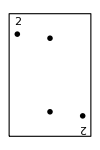
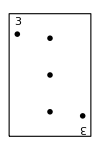
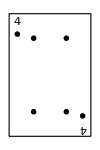
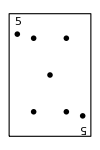
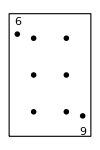
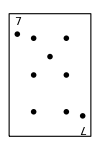
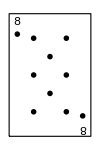
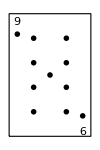
-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[ResourceFunction["PlayingCardGraphic"][10,ImageSize->Scaled[0.048]]ResourceFunction["PlayingCardGraphic"][23,ImageSize->Scaled[0.048]]]
```

Preparazione agli esercizi (2)

Per lo svolgimento degli esercizi, abbiamo bisogno di fornire delle definizioni di coppia e tris.
Una coppia si forma quando tra le carte scoperte sono presenti due carte con lo stesso valore e seme diverso, come nel seguente caso:

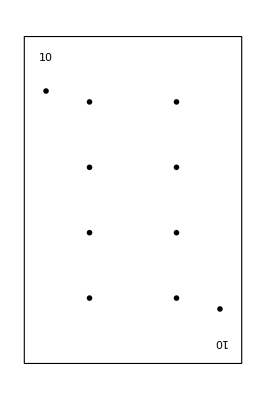
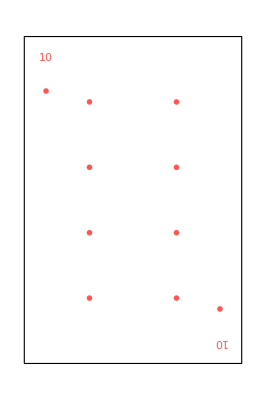

```mathematica
Print[ResourceFunction["PlayingCardGraphic"][10,ImageSize->Scaled[0.048]]ResourceFunction["PlayingCardGraphic"][23,ImageSize->Scaled[0.048]] ResourceFunction["PlayingCardGraphic"][36,ImageSize->Scaled[0.048]]]
```

Un tris invece si forma quando tra le carte scoperte sono presenti tre carte con lo stesso valore e seme diverso, come nel seguente caso:

-Graphics- -Graphics- -Graphics-

Una volta comprese le definizioni di coppia e tris, possiamo mostrare e descrivere le varie modalità.

## Modalità 1: Calcolo probabilità di una Coppia con una singola carta da scoprire (1)

La prima modalità consiste nel calcolare la probabilità che esca una coppia rivelando solo una carta del banco.
Una coppia si forma quando tra le tue carte e quelle scoperte sul banco ci sono due carte con lo stesso numero e segno diverso. 
Ad esempio:

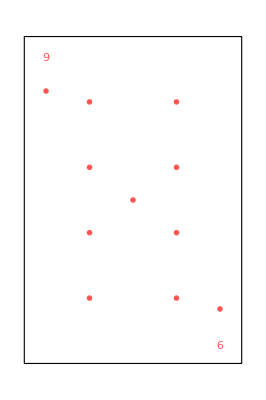
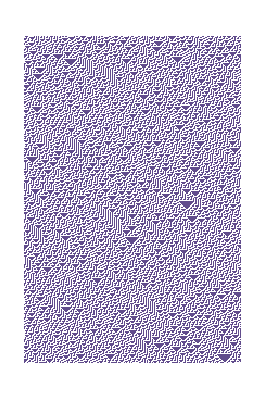
-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->Scaled[0.040]],"  ",ResourceFunction["PlayingCardGraphic"][22,ImageSize->Scaled[0.040]],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->Scaled[0.040]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.040]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.040]] }]]
```

```mathematica
Print[Grid[{{ResourceFunction["PlayingCardGraphic"][{8,48},"CardSpreadAngle"->0.3,ImageSize->Scaled[0.08]]}}]]
```

-Graphics-

Come possiamo notare, abbiamo una coppia di “9”, essendoci tra il banco (le carte sopra) e la nostra mano (le carte sotto) due carte con valore 9. 
In questo caso quindi, la probabilità che esca una coppia di 9 estraendo la prossima carta è 1, avendo già una coppia tra le carte scoperte.

## Modalità 1: Calcolo probabilità di una Coppia con una singola carta da scoprire (2)

Nel caso in cui invece non ci sia già una coppia tra le carte scoperte e ci viene chiesto di calcolare la probabilità che esca una coppia di una delle carte scoperte, la probabilità sarà uguale al numero di casi favorevoli fratto il numero di casi totali, ovvero il numero di 
carte restanti con quel valore numerico fratto il numero di carte restanti nel mazzo.

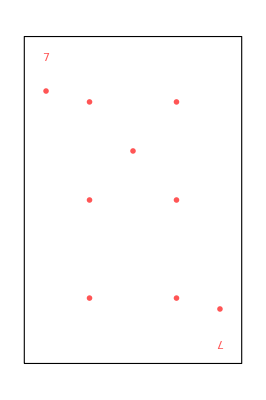
-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->Scaled[0.04]],"  ",ResourceFunction["PlayingCardGraphic"][20,ImageSize->Scaled[0.04]],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->Scaled[0.04]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.04]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.04]] }]]
```

```mathematica
Print[Grid[{{ResourceFunction["PlayingCardGraphic"][{8,48},"CardSpreadAngle"->0.3,ImageSize->Scaled[0.08]]}}]]
```

-Graphics-

In questo caso ad esempio, la probabilità che esca una coppia di “9” è uguale a numero di casi favorevoli fratto numero di casi totali. 
Rimangono ancora tre “9” nel mazzo, e le carte coperte restanti sono 52-5 = 48. La probabilità sarà quindi uguale a 3/48.

## Modalità 2: Calcolo probabilità di un Tris con 2 carte da scoprire

La seconda modalità consiste nel calcolare la probabilità di fare un tris estraendo le due carte coperte rimanenti. 
Un Tris si forma quando si hanno 3 carte dello stesso numero tra le carte sul banco e le carte nella mano del giocatore.
Per calcolare la probabilità è necessario controllare alcuni casi particolari, come ad esempio il caso in cui non ci sia alcuna coppia tra le carte scoperte e ci sia solo una carta coperta. In quel caso la probabilità è 0. 
Invece, se è già presente un tris tra le carte del banco e quelle del giocatore, la probabilità sarà 1.

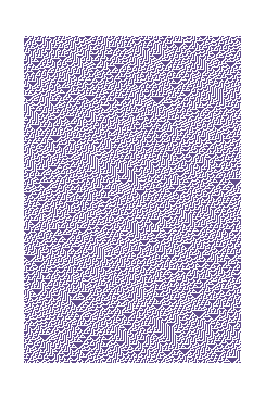
-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->Scaled[0.042]],"  ",ResourceFunction["PlayingCardGraphic"][22,ImageSize->Scaled[0.042]],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->Scaled[0.042]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.042]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.042]] }]]
```

```mathematica
Print[Grid[{{ResourceFunction["PlayingCardGraphic"][{8,48},"CardSpreadAngle"->0.3,ImageSize->Scaled[0.09]]}}]]
```

-Graphics-

A differenza della prima modalità, gli esercizi prenderanno in considerazione due carte da rivelare invece di una sola. 
Il tutto si riduce quindi al calcolo della probabilità che le carte coperte rimanenti siano per noi carte “favorevoli”, ovvero che ci permettano di avere un tris con le carte già scoperte.

## Modalità 3: Calcolo probabilità di una Coppia con 2 carte da scoprire

La terza modalità consiste nel calcolare la probabilità di fare una coppia rivelando le prossime due carte.

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->Scaled[0.042]],"  ",ResourceFunction["PlayingCardGraphic"][20,ImageSize->Scaled[0.042]],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->Scaled[0.042]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.042]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.042]] }]]
```

-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[Grid[{{ResourceFunction["PlayingCardGraphic"][{8,48},"CardSpreadAngle"->0.3,ImageSize->Scaled[0.09]]}}]]
```

-Graphics-

Questa modalità è molto simile alla modalità precedente, ma per creare una coppia basta solo una seconda carta dello stesso numero. 
Bisognerà quindi stare più attenti a come quel numero viene estratto tra le carte coperte che  rimangono.
Se ad esempio ci viene richiesta la probabilità che esca una coppia con una carta che abbiamo in mano e 3 carte ancora da estrarre, 
la probabilita risultante sarà la somma della probabilità che esca nella prima più quella che esca nella seconda e nella terza.

## Modalità 4: Calcolo probabilità di una Coppia estraendo le carte rimanenti, considerando anche gli avversari

La quarta modalità consiste nel calcolare la probabilità di fare una coppia estraendo le prossime due carte e considerando anche le carte degli avversari.

```mathematica
Print[Grid[{{ResourceFunction["PlayingCardGraphic"][{22,45},"CardSpreadAngle"->0.3,ImageSize->Scaled[0.073]]}}]]
```

Carte degli avversari :

-Graphics-

```mathematica
Print[Row[{ResourceFunction["PlayingCardGraphic"][10,ImageSize->Scaled[0.042]],"  ",ResourceFunction["PlayingCardGraphic"][20,ImageSize->Scaled[0.042]],"  ",ResourceFunction["PlayingCardGraphic"][39,ImageSize->Scaled[0.042]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.042]],"  ", ResourceFunction["PlayingCardGraphic"][0,ImageSize->Scaled[0.042]] }]]
```

Carte del banco :

-Graphics-  -Graphics-  -Graphics-  -Graphics-  -Graphics-

```mathematica
Print[Grid[{{ResourceFunction["PlayingCardGraphic"][{8,48},"CardSpreadAngle"->0.3,ImageSize->Scaled[0.09]]}}]]
```

Carte del giocatore:

-Graphics-

In questa modalità il giocatore dovrà anche controllare le carte degli avversari.  Infatti, essi potrebbero avere delle carte che serviranno  per comporre la coppia richiesta. Questo riduce i casi favorevoli. Ad esempio, nell’esercizio mostrato sopra, se ci viene richiesto di comporre una coppia di “9” dovremmo tener conto del fatto che il nostro avversario ha un “9” nella sua mano. 
Ciò riduce i casi favorevoli da 3 a 2.

## Prova tu!

Premi il bottone sottostante per iniziare a provare tu stesso.
Verrà aperta una nuova finestra nella quale basterà andare nella sezione “Evaluation” e selezionare “Evaluate Notebook” come nell’immagine seguente:


-Graphics-

Buon divertimento!

```mathematica
SetDirectory[NotebookDirectory[]];
Print[Button["GIOCA",NotebookOpen[NotebookDirectory[]<>"Main.nb"],
ImageSize->{300,200},
BaseStyle->{FontSize->66,FontFamily->"Impact", FontColor->Red}]]
```

GIOCA